```mathematica
stokeslet[x_,e_]:= 3/400 (e+Dot[x,e]x/Norm[x]^2)/Norm[x];
dipole[x_,d_,e_]:= 3/400((Dot[x,d]e-Dot[e,x]d-Dot[d,e]x)/Norm[x]+(3Dot[e,x]Dot[d,x]x)/Norm[x]^3)/Norm[x]^2;
doublet[x_,e_]:=3/400(-e+3Dot[e,x]x/Norm[x]^2)/Norm[x]^3;blakelet[x_,y_,e_]:= stokeslet[y-x,e]+(-stokeslet[y-(x-{0,2 x[[2]]}),{1,0}] +2x[[2]]dipole[y-(x-{0,2 x[[2]]}),{1,0},{0,1}]-2x[[2]]^2 doublet[y-(x-{0,2 x[[2]]}),{1,0}])e[[1]] + (-stokeslet[y-(x-{0,2 x[[2]]}),{0,1}] +2x[[2]]dipole[y-(x-{0,2 x[[2]]}),{0,1},{0,1}]-2x[[2]]^2 doublet[y-(x-{0,2 x[[2]]}),{0,1}])e[[2]];
```

```mathematica
xx[t_]={Cos[t-Pi/2],Sin[t-Pi/2]+2};
xx[0]
```

{0,1}

```mathematica
xxdot[t_]=N[D[xx[t],t]];
```

```mathematica
f[y_,t_]=blakelet[xx[t],y,xxdot[t]];
f2[y1_,y2_,t_]=blakelet[xx[t],{y1,y2},xxdot[t]];
```

```mathematica
VectorPlot[f2[x1,x2,0],{x1,-15,15},{x2,0.001,10},PlotRange->{{-15,15},{0,10}},AspectRatio->1/2];
```

```mathematica
{yy1,yy2}=NDSolveValue[{{y1'[t],y2'[t]}==f2[y1[t],y2[t],t],y1[0]==0,y2[0]==0.95},{y1,y2},{t,0,2Pi}];
```

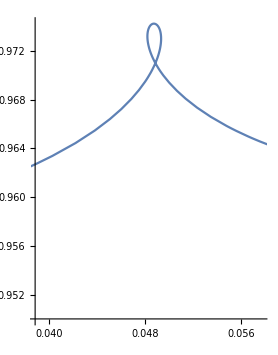

```mathematica
ParametricPlot[{yy1[t],yy2[t]},{t,0,2Pi}]
```

```mathematica
tracer=ParametricNDSolveValue[{{y11'[t],y22'[t]}==f2[y11[t],y22[t],t],y11[0]==b1,y22[0]==b2},{y11[2Pi]-y11[0],y22[2Pi]-y22[0]},{t,0,2Pi},{b1,b2},Method->StiffnessSwitching];
```

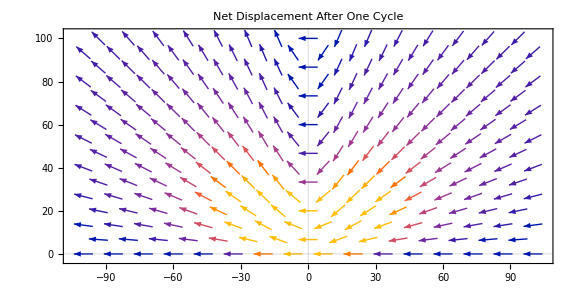

```mathematica
VectorPlot[tracer[p,q],{p,-100,100},{q,0,100},PlotTheme->"Scientific",PlotLabel->"Net Displacement After One Cycle",AspectRatio->1/2,ImageSize->Large]
```

```mathematica
stokeslet2[x_,y_,e_]:= 3/40 (e+Dot[y-x,e](y-x)/Norm[y-x]^2)/Norm[y-x];
g[y_,t_]=stokeslet2[xx[t],y,xxdot[t]];
g2[y1_,y2_,t_]=stokeslet2[xx[t],{y1,y2},xxdot[t]];
```

```mathematica
tracer2=ParametricNDSolveValue[{{y111'[t],y222'[t]}==stokeslet2[xx[t],{y111[t],y222[t]},xxdot[t]],y111[0]==c1,y222[0]==c2},{y111[2Pi]-y111[0],y222[2Pi]-y222[0]},{t,0,2Pi},{c1,c2}];
tracer2[3,1]
```

{0.0139238,0.0451355}

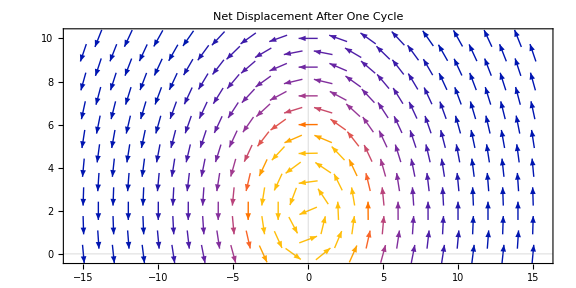

```mathematica
VectorPlot[tracer2[p,q],{p,-15,15},{q,0,10},PlotTheme->"Scientific",PlotLabel->"Net Displacement After One Cycle",AspectRatio->1/2,ImageSize->Large]
```

```mathematica
{yyy1,yyy2}=NDSolveValue[{{y111'[t],y222'[t]}==stokeslet2[xx[t],{y111[t],y222[t]},xxdot[t]],y111[0]==0,y222[0]==0.4},{y111,y222},{t,0,2Pi},Method->StiffnessSwitching];
```

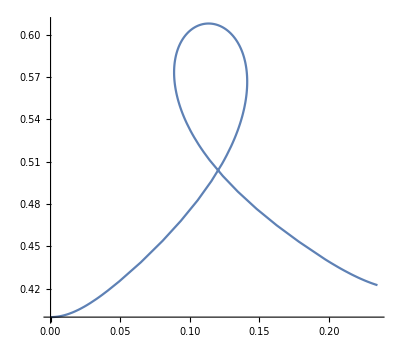

```mathematica
ParametricPlot[{yyy1[t],yyy2[t]},{t,0,2Pi}]
```

```mathematica
approxlet[a_,b_,c_] := N[(3/400) (Dot[a,c]a /(Norm[a]^2) - (Dot[a,a]^(-1))(1-(4Dot[a,{0,b[[2]]}]/(Dot[a,a]))Dot[a+{0,2b[[2]]},c](a+{0,2b[[2]]})))]
```

```mathematica
displacementTest2[p_,q_] := NIntegrate[approxlet[{p,q},xx[t],xxdot[t]],{t,0,2Pi}]
```

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

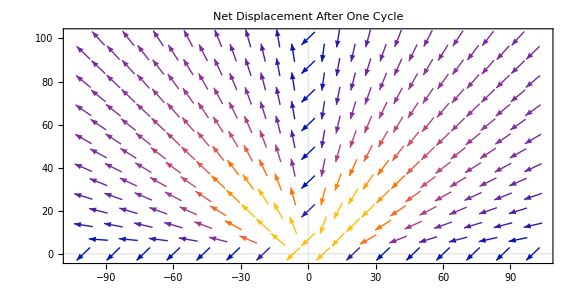

```mathematica
VectorPlot[displacementTest2[p,q],{p,-100,100},{q,0,100},PlotTheme->"Scientific",PlotLabel->"Net Displacement After One Cycle",AspectRatio->1/2,ImageSize->Large]
```

```mathematica
N[approxlet[{1,1},xx[0],xxdot[0]]]
```

{0.0132583,0.0344715}